### Supplementary code for simulations of D. suzukii population dynamics in “Large-scale open field trials in California and Oregon to evaluate the potential use of a new behavioral control system for Drosophila suzukii Matsumura (Diptera: Drosophilidae)” by Tait et al. (2022) Contact for code: ferdinand.pfab@gmail.com This file loads the temperature data

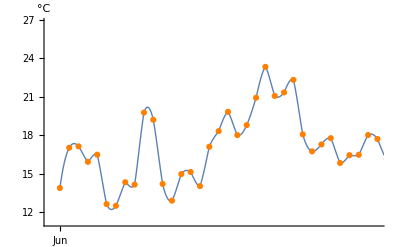

```mathematica
(*load the temperature file - this file needs to be in the same directory as this notebook*)
weatherfile=Import[NotebookDirectory[]<>"Oregon Aurora Weather 2020.xlsx"];
(*convert to list of daily mean temperatures*)
meantemplist=Mean/@ToExpression[(StringSplit[#,","]&/@weatherfile[[1,16;;138,2]])[[All,{2,3}]]];
(*functions to convert from Fahrenheit to Celsius and vice versa*)
celsius[fahrenheit_]:=(fahrenheit−32)×5/9;
fahrenheit[celsius_]:=celsius×9/5+32;
(*the daily mean temperatures in Celsius*)
weatherlist=Round[celsius/@meantemplist,10^-3];
(*how many days before day zero to start the temperature function*)
adddays=0;
(*interpolation of the mean temperatures*)
w=Interpolation[Transpose[{Range[Length@#]-adddays,#}&@Flatten[{Table[N@weatherlist[[1]],adddays],weatherlist}]]];
(*total number of days we have temperature data for*)
totaldays=Length[weatherlist];
(*lengths of month of year*)
monthlength={31,28,31,30,31,30,31,31,30,31,30,31};
(*names of months of year*)
monthnames={"Jan","Feb","Mar","Apr","May","Jun","Jul","Aug","Sep","Oct","Nov","Dec"};
(*labels for time axis*)
startmonth=6;
endmonth=11;
xlabelsmonth=Table[{1+Total[monthlength[[startmonth;;startmonth+j-1]]],monthnames[[j+startmonth]]},{j,0,endmonth-startmonth}];
(*show temperature data and interpolation function*)
Show[Plot[w[t],{t,1,85},PlotStyle->Thick],ListPlot[weatherlist,PlotMarkers->Automatic,PlotStyle->{Orange,PointSize[Medium]}],LabelStyle->20,
PlotRangePadding->0,
ImageSize->400, 
AxesOrigin->{1,0},
PlotRange->{{0,35},Automatic},
Ticks->{xlabelsmonth,Automatic},
AxesLabel->{None,"°C"}]
```